# In-Class NullCline Examples

## Example #1

Let’s begin by considering the following system.  

ẋ = y
ẏ =2 - y - sin(x),   x∈[0,2π), y∈ℝ

Let’s plot the phase-plane along with the nullclines.  Here, the x-nullcline is given by y = 0, and the y nullcline is given by y = 2 - sin(x).

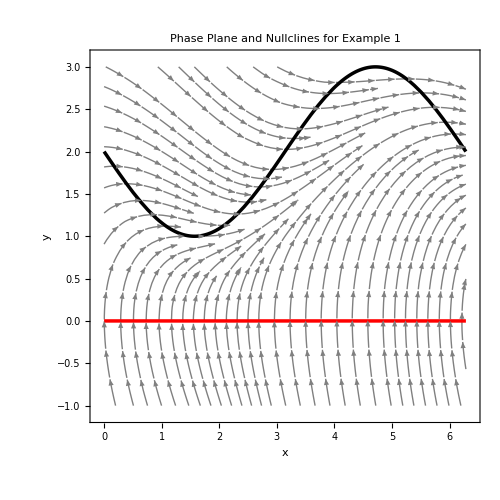

```mathematica
f = y;
g = 2 - y - Sin[x];p1=StreamPlot[{f,g},{x,0,2π},{y,-1,3},ImageSize->500,StreamStyle->Gray,StreamPoints->60,StreamScale->0.05];
p2=Plot[{0,2-Sin[x]},{x,0,2π},PlotStyle->{{Red,Thickness->0.005},{Black,Thickness->0.005}}];
Show[p1,p2,FrameLabel->{"x","y"},PlotLabel->"Phase Plane and Nullclines for Example 1"]
```

## Example #2

Now, let’s consider the system given by 

ẋ = x^2-1
ẏ =a(x^2-1) - x y,                     x,y∈ℝ, a≥0.

We can construct a manipulate to plot the phase plane and nullclines as we vary the parameter a.
Here, the x-nullclines are given by x = ±1, and the y-nullclines are given by  y = 0, x = 0 if a = 0, or y = a(x^2-1)/x if a>0.

```mathematica
f2 = x^2-1;
g2[a_] = a(x^2-1) - x y;
eqPts = Solve[{f2==0,g2[a]==0},{x,y}];
Manipulate[
p1=StreamPlot[{f2,g2[a]},{x,-2,2},{y,-2,2},ImageSize->500,StreamStyle->Gray,StreamPoints->40,StreamScale->0.05];
If[a>0,
p2=ParametricPlot[{{x,a (x^2-1)/x},{-x,-a (x^2-1)/x}},{x,(-1+√(1+a^2))/a,2},PlotStyle->{{Red,Thickness->0.005}},PlotRange->{-3,3}],
p2=ParametricPlot[{{0,t},{t,0}},{t,-2,2},PlotStyle->{{Red,Thickness->0.005}}]];
p3=ParametricPlot[{{1,t},{-1,t}},{t,-2,2},PlotStyle->{{Black,Thickness->0.005}}];
eqPtsPlot = ListPlot[{x,y}/.eqPts,
PlotMarkers->{Automatic,Scaled[.02]},
PlotStyle->Black];
Show[p1,p2,p3,eqPtsPlot,PlotRange->{-2,2},FrameLabel->{"x","y"},PlotLabel->"Phase Plane and Nullclines for Example 2"],
{a,0,.2}]
```